# STROŠKI OLIMPIJSKIH IGER

## Analiza stroškov olimpijskih iger in držav gostiteljic med leti 1964 in 2016

## Pridobivanje podatkov

Mathematica ima na voljo veliko podatkovno bazo Wolfram data repository.

```mathematica
ResourceSearch["Olympic Games"]
```

{ResourceObject[…]}

Shranimo podatke:

```mathematica
vsiPodatki = ResourceData["Olympic Games Costs"]
```

Dataset[<>]

Tiste olimpijske igre, za katere ni bilo podatkov o stroških, sem izbrisal iz tabele. Tam, kjer bom analiziral stroške, jih ne bom upošteval.

```mathematica
podatki = Select[vsiPodatki, !MissingQ[#Cost]&];
```

```mathematica
poletneIgre = Select[podatki, #["Type"] ==  "Summer" &];
```

```mathematica
zimskeIgre = Select[podatki, #["Type"] ==  "Winter" &];
```

## Analiza stroškov

Spodaj vidimo diagrama, ki predstavljata stroške na posameznih olimpijskih igrah. Pričakoval sem, da bodo stroški pri kasnejših igrah višjji.

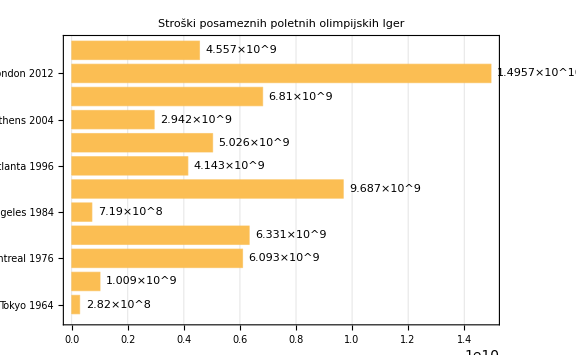

```mathematica
BarChart[poletneIgre[All, "Cost"], ChartLabels->{poletneIgre[All, "Games"]//Normal},LabelingFunction->After, PlotLabel->"Stroški posameznih poletnih olimpijskih Iger", ImageSize->Large, BarSpacing->Medium, PlotTheme->"Detailed", BarOrigin->Left]
```

Zgoraj vidimo, kakšni so bili stroški posameznih poletnih olimpijskih iger. Daleč najvišji so bili leta 2012 v Londonu. Moja hipoteza, da bodo stroški pri kasnejših igrah višji, ni pravilna. Že, na primer,  leta 1976 so bili stroški višji kot leta 2016, in celo dvakrat višji kot leta 2004.

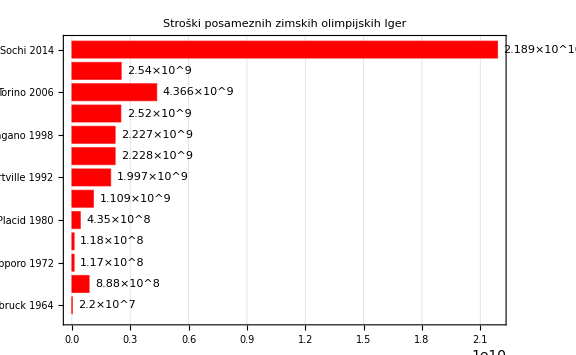

```mathematica
BarChart[zimskeIgre[All, "Cost"], ChartLabels->{zimskeIgre[All, "Games"]//Normal},LabelingFunction->After, PlotLabel->"Stroški posameznih zimskih olimpijskih Iger", ImageSize->Large, BarSpacing->Medium, PlotTheme->"Detailed", ChartStyle->{Red}, BarOrigin->Left]
```

Diagram s stroški zimskih olimpijskih iger je bolj tak, kot sem pričakoval. Torej, na kasnejših olimpijskih igrah so bili večinoma višji stroški. Vidimo tudi, da so si stroški različnih iger dokaj blizu, zelo odstopajo le igre leta 2014 v Sočiju.

Sedaj bom stroške zimskih in poletnih iger združil v en graf. Točke bom med sabo povezal, da se bo lepše videlo razliko v stroških. Vidimo, da so bili stroški na poletnih igrah višji kot na zimskih. Izjema je Soči leta 2014, ki je v tej kategoriji daleč pred vsemi.

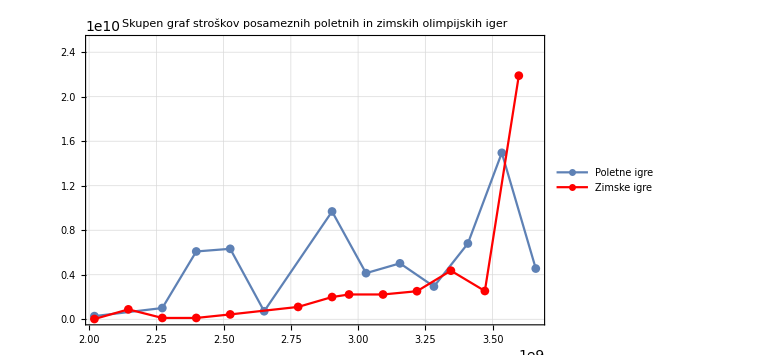

```mathematica
Show[DateListPlot[poletneIgre[All, {"Year", "Cost"}], PlotTheme->"FullAxesGrid",PlotRange->{0, 2.5*10^10},PlotLegends->LineLegend[{"Poletne igre"}], PlotMarkers->Automatic], 
DateListPlot[zimskeIgre[All, {"Year", "Cost"}], PlotTheme->"FullAxesGrid", PlotRange->{0, 2.5*10^10}, PlotLegends->LineLegend[{"Zimske igre"}], PlotStyle->Red, PlotMarkers->Automatic],
PlotLabel->"Skupen graf stroškov posameznih poletnih in zimskih olimpijskih iger", ImageSize->Large]
```

Iz grafa vidimo, da so bili najnižji stroški leta 1964 v Innsbrucku, najvišji pa 2014 v Sočiju. To lahko tudi preverimo:

```mathematica
Select[podatki,#["Cost"] == Min[podatki[All, "Cost"]]&][1, "Games"]
```

Innsbruck 1964

```mathematica
Select[podatki,#["Cost"] == Max[podatki[All, "Cost"]]&][1, "Games"]
```

Sochi 2014

Da so stroški poletnih olimpijskih iger veliko višji, je razumljivo, saj lahko vidimo, da je poleti tudi veliko več dogodkov:

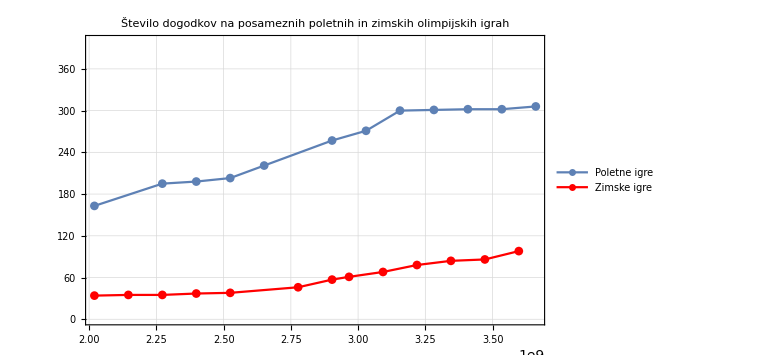

```mathematica
Show[DateListPlot[poletneIgre[All, {"Year", "Events"}], PlotLabel->"Število dogodkov na posameznih poletnih olimpijskih igrah", PlotTheme->"FullAxesGrid", PlotRange->{0, 400},PlotLegends->LineLegend[{"Poletne igre"}], PlotMarkers->Automatic],
DateListPlot[zimskeIgre[All, {"Year", "Events"}],  PlotLabel->"Število dogodkov na posameznih zimskih olimpijskih igrah", PlotTheme->"FullAxesGrid", PlotRange->{0, 400},PlotLegends->LineLegend[{"Zimske igre"}], PlotStyle->Red, PlotMarkers->Automatic],
PlotLabel->"Število dogodkov na posameznih poletnih in zimskih olimpijskih igrah", ImageSize->Large]
```

Kaj pa stroški na dogodek?
V podatkih manjka podatek o stroških na dogodek na olimpijskih igrah v Sočiju. Zato najprej dopolnimo podatke. Ker vemo, kolikšni so bili v Sočiju absolutni stroški, in koliko je bilo dogodkov, lahko izračunamo tudi stroške na dogodek.

```mathematica
stroskiRusija = Round[Select[podatki, #["Games"] ==  "Sochi 2014" &][1, "Cost"] / Select[podatki, #["Games"] ==  "Sochi 2014" &][1, "Events"]]
```

223367347 $

Dodajmo našim podatkom še stroške na dogodek v Sočiju:

```mathematica
niz = Normal[zimskeIgre[All, {"Games", "Year", "CostPerEvent"}]];
```

Ker v seznamu manjka samo en podatek, ga lahko zamenjamo kar tako:

```mathematica
popravljeno = ReplacePart[niz, Position[niz,Missing["NotAvailable"]]-> stroskiRusija];
```

Vse skupaj samo še spremenimo v tabelo:

```mathematica
tabelaZimskihStroskovNaDogodek = Dataset[popravljeno];
```

Sedaj lahko narišemo graf, ki predstavlja stroške na dogodek na posameznih igrah. Ker olimpijske igre v Sočiju zelo izstopajo, bom narisal dva grafa. Na prvem se bo videla cela slika, na drugem pa bo graf povečan in se ne bo videlo do kam grejo stroški v Sočiju.

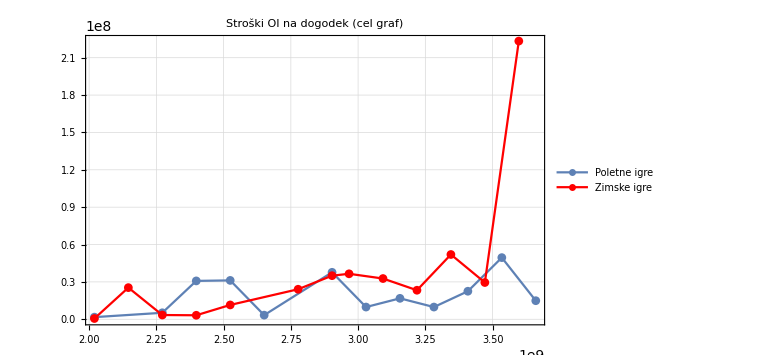

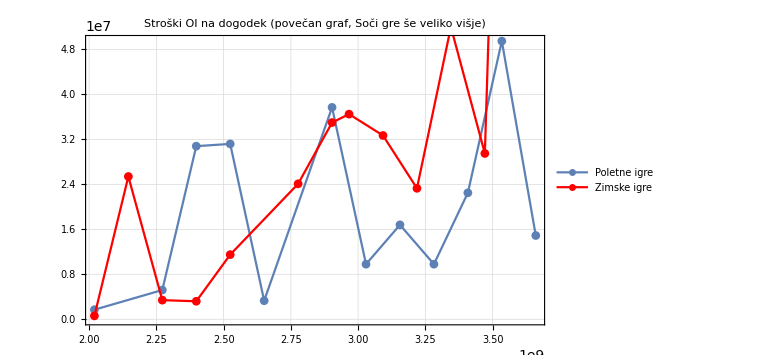

```mathematica
a1 = DateListPlot[poletneIgre[All, {"Year", "CostPerEvent"}], PlotLabel->"Stroški poletnih olimpijskih iger na posamezni dogodek", PlotTheme->"FullAxesGrid", ImageSize->Medium,PlotLegends->LineLegend[{"Poletne igre"}], PlotMarkers->Automatic];
a2 = DateListPlot[tabelaZimskihStroskovNaDogodek[All, {"Year", "CostPerEvent"}], PlotLabel->"Stroški zimskih olimpijskih iger na posamezni dogodek", PlotTheme->"FullAxesGrid", ImageSize->Medium,PlotRange->{0, 223367347}, PlotLegends->LineLegend[{"Zimske igre"}], PlotStyle->Red, PlotMarkers->Automatic];
Show[a1, a2,PlotLabel->"Stroški OI na dogodek (cel graf)", PlotRange->{0, 223367347},ImageSize->Large]
Show[a1, a2, PlotLabel-> "Stroški OI na dogodek (povečan graf, Soči gre še veliko višje)",ImageSize->Large]
```

Grafa se veliko sekata, torej vidimo, da so stroški na dogodek bolj primerljivi. Olimpijske igre v Sočiju sedaj izstopajo še veliko bolj kot pri absolutnih stroških.

Radi bi videli še, kje so bili stroški na dogodek najnižji.
Najprej, v tabelo (kjer so vse olimpijske igre med letoma 1960 in 2016, ki imajo podatke o stroških) vstavimo stroške na dogodek iz Sočija.

```mathematica
tabelaVsehStroškovNaDogodek= Dataset[ReplacePart[Normal[podatki[All, {"Games", "Year", "CostPerEvent"}]], Position[Normal[podatki[All, {"Games", "Year", "CostPerEvent"}]],Missing["NotAvailable"]]-> stroskiRusija]];
```

Sedaj lahko pogledamo, kje so bili stroški na dogodek najnižji in kje najvišji.

```mathematica
Select[tabelaVsehStroškovNaDogodek,#["CostPerEvent"] == Min[tabelaVsehStroškovNaDogodek[All, "CostPerEvent"]]&][1, "Games"]
```

Innsbruck 1964

```mathematica
Select[tabelaVsehStroškovNaDogodek,#["CostPerEvent"] == Max[tabelaVsehStroškovNaDogodek[All, "CostPerEvent"]]&][1, "Games"]
```

Sochi 2014

Vidimo, da so bili stroški na dogodek najvišji in najnižji na istih igrah, kot so bili absolutni stroški.

## Gostiteljice olimpijskih iger med leti 1960 in 2016

V spodnji tabeli so vse države, ki so gostile olimpijske igre med letoma 1960 in 2019.

```mathematica
vsiPodatki[Select[Head[#["Country"]]=!=Failure&],"Country"]
```

Dataset[<>]

V tabeli so vse države, ki še obstajajo. Kot vidimo ni Sovjetske zveze in Jugoslavije.

```mathematica
seznamDrzav=Select[vsiPodatki, !MissingQ[#CountryEntity]&][Select[Head[#["CountryEntity"]]=!=Failure&],"CountryEntity"]
```

Dataset[<>]

Spodaj vidimo, koliko olimpijskih iger med letoma 1960 in 2016, je gostila posamezna država.

```mathematica
gostiteljice[drzava_]:={drzava,Count[seznamDrzav,drzava]}
```

```mathematica
kolikokratGostiteljice=gostiteljice/@(seznamDrzav//DeleteDuplicates)
```

Dataset[<>]

Tabelo spremenimo v seznam.

```mathematica
Normal[kolikokratGostiteljice]
```

{{Italy,2},{Japan,3},{Mexico,1},{Germany,1},{Canada,3},{United States,5},{South Korea,1},{Spain,1},{Australia,1},{Greece,1},{China,1},{United Kingdom,1},{Brazil,1},{Austria,2},{France,2},{Norway,1},{Russia,1}}

Seznam popravimo ročno. Dvoje igre v zgornjem seznamu še manjkajo, saj državi, ki sta jih gostili ne obstajata več. Za igre iz Sovjetske zveze bomo rekli, da so bile v Rusiji, saj je bila gostiteljica Moskva. Za igre iz Jugoslavije pa sem vzel kar Bosno in Hercegovino, saj so bile takrat igre v Sarajevu.

```mathematica
seznamGostiteljic = {Entity["Country","Italy"]-> 2,Entity["Country","Japan"]-> 3,Entity["Country","Mexico"]-> 1,Entity["Country","Germany"]-> 1,Entity["Country","Canada"]-> 3,Entity["Country","UnitedStates"]-> 5,Entity["Country","SouthKorea"]-> 1,Entity["Country","Spain"]-> 1,Entity["Country","Australia"]-> 1,Entity["Country","Greece"]-> 1,Entity["Country","China"]-> 1,Entity["Country","UnitedKingdom"]-> 1,Entity["Country","Brazil"]-> 1,Entity["Country","Austria"]-> 2,Entity["Country","France"]-> 2,Entity["Country","Norway"]-> 1,Entity["Country","Russia"]-> 2, Entity["Country","BosniaHerzegovina"]-> 1};
```

Na spodnjem zemljevidu vidimo katere države so gostile olimpijske igre med letoma 1960 in 2016, ter katere so jih gostile večkrat.

```mathematica
GeoRegionValuePlot[seznamGostiteljic, GeoRange->"World", GeoProjection->"Mercator", ImageSize-> Large, GeoBackground->"CountryBorders"]
```

-Graphics-

Poglejmo še, kolikokrat je olimpijske igre med letoma 1960 in 2016 gostila katera celina:

```mathematica
"Severna Amerika"-> Length[Select[vsiPodatki, MemberQ[EntityList[Entity["GeographicRegion","NorthAmerica"][EntityProperty["GeographicRegion","Countries"]]],#["CountryEntity"]]&]]
"Južna Amerika" ->  Length[Select[podatki, MemberQ[EntityList[Entity["GeographicRegion","SouthAmerica"][EntityProperty["GeographicRegion","Countries"]]],#["CountryEntity"]]&]]
"Evropa"->  Length[Select[podatki, MemberQ[EntityList[Entity["GeographicRegion","Europe"][EntityProperty["GeographicRegion","Countries"]]],#["CountryEntity"]]&]]
"Azija"->  Length[Select[podatki, MemberQ[EntityList[Entity["GeographicRegion","Asia"][EntityProperty["GeographicRegion","Countries"]]],#["CountryEntity"]]&]]
"Avstralija"->  Length[Select[podatki, MemberQ[EntityList[Entity["GeographicRegion","Australia"][EntityProperty["GeographicRegion","Countries"]]],#["CountryEntity"]]&]]
"Afrika"->  Length[Select[podatki, MemberQ[EntityList[Entity["GeographicRegion","Africa"][EntityProperty["GeographicRegion","Countries"]]],#["CountryEntity"]]&]]
```

Severna Amerika→9

Južna Amerika→1

Evropa→11

Azija→4

Avstralija→1

Afrika→0

Vidimo, da je olimpijske igre največkrat gostila Evropa, ki ji lahko dodamo še dvoje igre, saj Sovjetska zveza in Jugoslavija v zgornjih podatkih nista šteta. Vidimo pa lahko tudi, da Afrika (vsaj med letoma 1960 in 2016) še ni gostila olimpijskih iger.

## Analiza olimpijskih iger v ZDA

Vidimo, da so med letoma 1960 in 2016 olimpijske igre največkrat gostile Združene države Amerike. Gostile so jih petkrat.

```mathematica
Select[kolikokratGostiteljice,#[[2]]==Max[kolikokratGostiteljice[All,2]]&]
```

Dataset[<>]

V spodnji tabeli so vse olimpijske igre med letoma 1960 in 2016, ki so jih gostile ZDA.

```mathematica
usa = Select[vsiPodatki, #["CountryEntity"]==LinguisticAssistant &]
```

Dataset[<>]

ZDA so gostile dvoje poletne in tri zimske igre:

```mathematica
Length[Select[usa, #["Type"] ==  "Summer" &]]
```

2

```mathematica
Length[Select[usa, #["Type"] ==  "Winter" &]]
```

3

```mathematica
usapodatki =Select[usa, !MissingQ[#Cost]&];
```

```mathematica
"Najvišji stroški" -> Select[usapodatki,#["Cost"] == Max[usapodatki[All, "Cost"]]&][1, "Games"]
```

Najvišji stroški→Atlanta 1996

```mathematica
"Najvišji stroški na dogodek" ->Select[usapodatki,#["CostPerEvent"] == Max[usapodatki[All, "CostPerEvent"]]&][1, "Games"]
```

Najvišji stroški na dogodek→Salt Lake City 2002

```mathematica
"Najnižji stroški" ->Select[usapodatki,#["Cost"] == Min[usapodatki[All, "Cost"]]&][1, "Games"]
```

Najnižji stroški→Lake Placid 1980

```mathematica
"Najnižji stroški na dogodek" ->Select[usapodatki,#["CostPerEvent"] == Min[usapodatki[All, "CostPerEvent"]]&][1, "Games"]
```

Najnižji stroški na dogodek→Los Angeles 1984

Vidimo, da so bili najvišji in najnižji stroški ter najvišji in najnižji stroški na dogodek vedno na različnih olimpijskih igrah.  Za olimpijske igre v Squaw Valleyu ni podatkov o stroških. Glede na to, da so bile že leta 1960, so bili stroški verjetno nižji kot na ostalih igrah.

Vidimo lahko tudi, da so bile zadnje olimpijske igre v ZDA leta 2002.

```mathematica
Select[usapodatki,#["Year"] == Max[usapodatki[All, "Year"]]&][1, {"Games","Year"}]
```

Dataset[<>]

## Aplikacija v oblaku

```mathematica
prikazPodatkov[drzava_]:=If[MemberQ[ Normal[vsiPodatki[All, "CountryEntity"]], drzava], StringForm["Between 1960 and 2016 `` hosted Olympic Games `` time(s). There is a table with more data: ``",Select[ResourceData["Olympic Games Costs"], #["CountryEntity"]==drzava&][1, "Country"],Length[Select[ResourceData["Olympic Games Costs"], #["CountryEntity"]==drzava&]],Select[ResourceData["Olympic Games Costs"], #["CountryEntity"]==drzava&]], "This country didn't host Olympic Games between 1960 and 2016 "]
```

```mathematica
prikazPodatkov[Entity["Country","Italy"]]
```

Between 1960 and 2016 Italy hosted Olympic Games 2 time(s). There is a table with more data: …

```mathematica
obrazec = FormPage["drzava" -> "Country", prikazPodatkov[#drzava] &,AppearanceRules-><|"Title" -> "Gostitelji olimpijskih iger", "Description" -> "Vnesi ime drzave, za katero zelis izvedeti, kolikokrat je med leti 1960 in 2016 gostila olimpijske igre, ter podrobnosti teh iger.", "SubmitLabel" -> "Prikazi"|>]
```

```mathematica
CloudDeploy[obrazec, Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/64ec58bf-3775-45fe-93ab-fda1c5227b44]